```mathematica
If[ !ValueQ[allGraphs6],allGraphs6=Get["d:\\saved\\allGraphs6-fullfullgen.m"]]
```

## Now define the base basic data

```mathematica
Bases6=Association[];
```

```mathematica
Bases6["C"]=Association[];
```

```mathematica
Bases6["C","Colofour"]="colofour";
```

```mathematica
Bases6["E"]=Association[];
```

```mathematica
Bases6["E","Colofour"]="colofourrealnull";
```

```mathematica
Bases6["G"]=Association[];
```

```mathematica
Bases6["G","Colofour"]="colofourgenerator";
```

```mathematica
Bases6["F"]=Association[];
```

```mathematica
Bases6["F","Colofour"]="colofournull";
```

```mathematica
allBases6=Keys[Bases6]
```

{C,E,G,F}

## Working with bases

```mathematica
MyComp:=CompareSymbols;
```

```mathematica
Table[Bases6[base,"AtomKeys"]=Sort[Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,Bases6[base,"Colofour"]]]]==1&],MyComp[allGraphs6[#1,Bases6[base,"Colofour"]],allGraphs6[#2,Bases6[base,"Colofour"]]]&]
,{base,allBases6}];
```

```mathematica
Table[Bases6[base,"Variables"]=Table[allGraphs6[k,Bases6[base,"Colofour"]],{k,Bases6[base,"AtomKeys"]}]
,{base,allBases6}];
```

```mathematica
BaseFormula6[key_,base_]:=allGraphs6[key,Bases6[base,"Colofour"]]
```

```mathematica
BaseCoeff6[key_,base_]:=Table[Coefficient[allGraphs6[key,Bases6[base,"Colofour"]],var],{var,Bases6[base,"Variables"]}]
```

```mathematica
BaseCoeff6[0,"F"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix6[base1_,base2_]:=Table[BaseCoeff6[key1,base2],{key1,Bases6[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases6[base,"AtomKeys"],{base,allBases6}]//Flatten//DeleteDuplicates//Length
```

807

```mathematica
Clear[RepGraph6];RepGraph6[base_]:=RepGraph6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ShowGraph[allGraphs6,key],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepKey6];RepKey6[base_]:=RepKey6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->key,{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial6];RepChromial6[base_]:=RepChromial6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ChromaticPolynomial[allGraphs6[key,"graph"],x],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepBase6];RepBase6[base_,base2_]:=RepBase6[base,base2]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->allGraphs6[key,Bases6[base2,"Colofour"]],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepLabel6];RepLabel6[base_]:=RepLabel6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->SymbolToLabel[allGraphs6[key,Bases6[base,"Colofour"]]],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
ConversionMatrix6["G","C"]==Transpose[ConversionMatrix6["E","C"]]
```

True

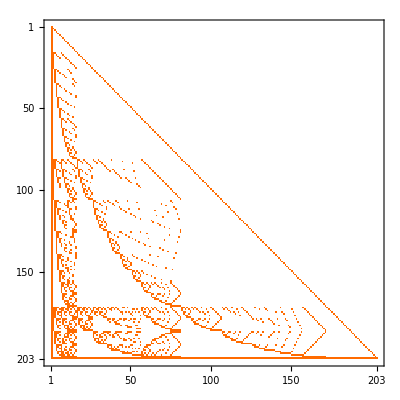

```mathematica
MatrixPlot[ConversionMatrix6["G","C"]]
```

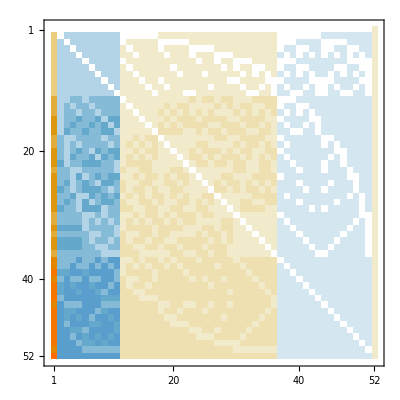

```mathematica
Inverse[ConversionMatrix["G","E"]]//MatrixPlot
```

```mathematica
ZeroOne[mat_]:=Map[Map[If[#==0,0,If[#<0,-1,1]]&,#]&,mat]
```

```mathematica
ConversionMatrix6["C","E"]==Transpose[ConversionMatrix6["C","G"]]
```

True

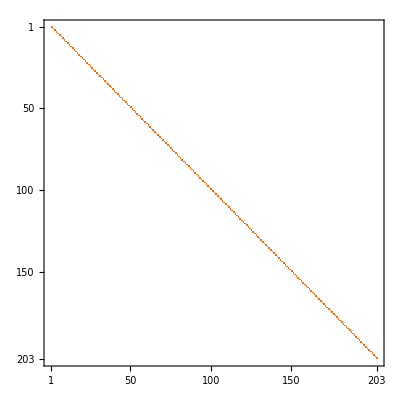
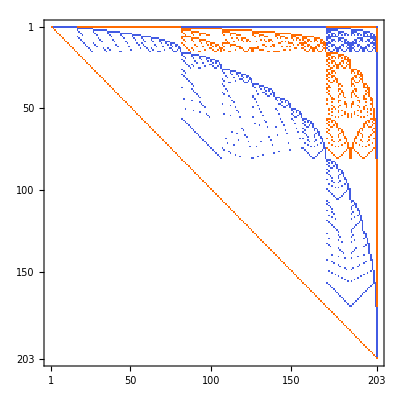
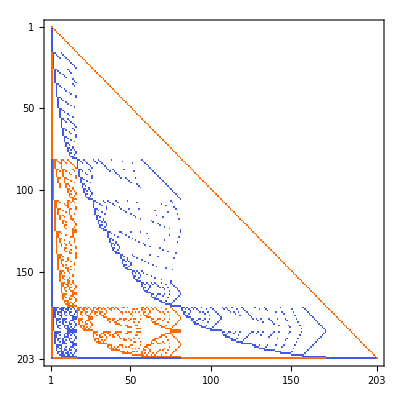
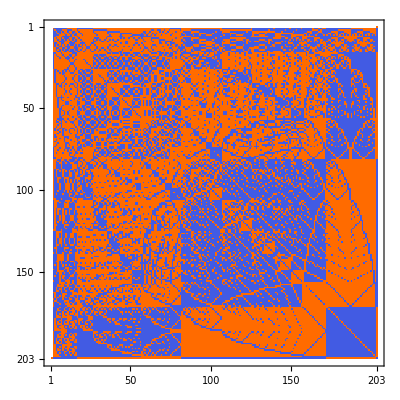
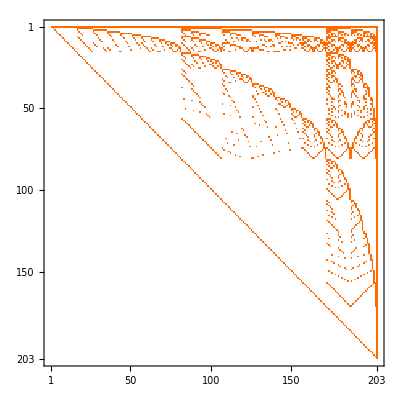
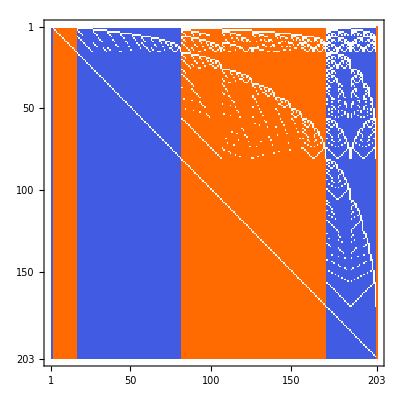
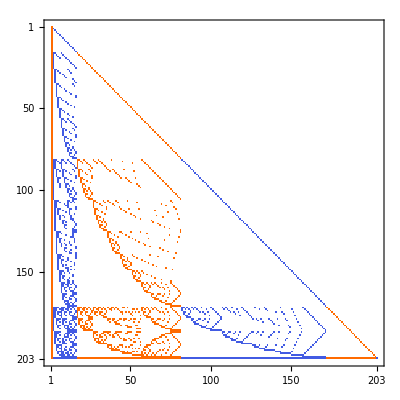
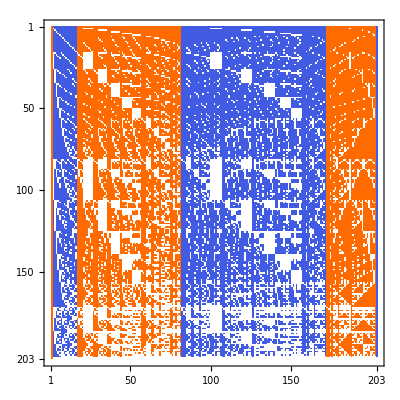
| C | E | G | F
C | -Graphics-C→C | -Graphics-C→E | -Graphics-C→G | -Graphics-C→F
E | -Graphics-E→C | -Graphics-E→E | -Graphics-E→G | -Graphics-E→F
G | -Graphics-G→C | -Graphics-G→E | -Graphics-G→G | -Graphics-G→F
F | -Graphics-F→C | -Graphics-F→E | -Graphics-F→G | -Graphics-F→F

```mathematica
TableForm[Table[
Labeled[MatrixPlot[ZeroOne[ConversionMatrix6[base1,base2]]],base1->base2]
,{base1, allBases6},{base2,allBases6}],TableHeadings->{allBases6, allBases6}]
```

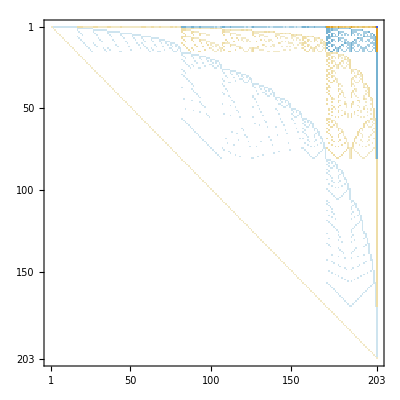
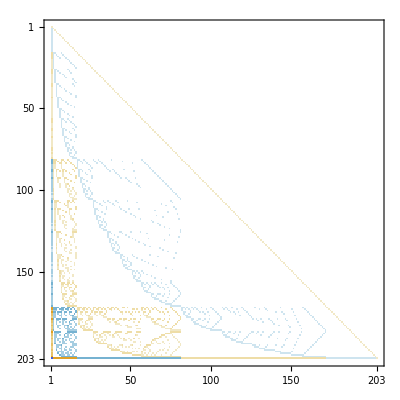
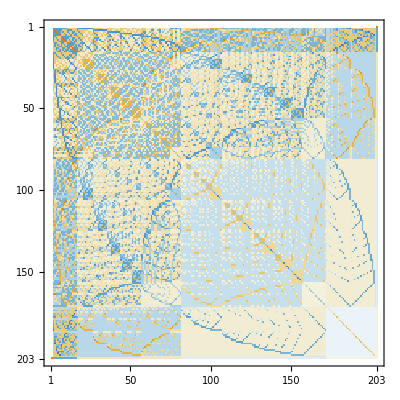
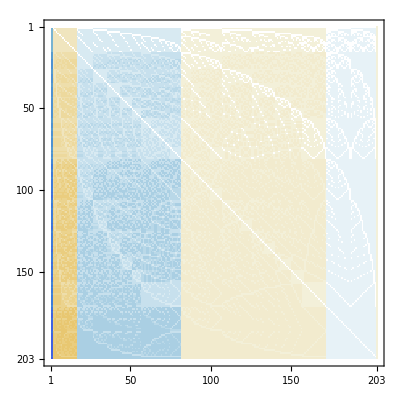
| C | E | G | F
C | -Graphics-C→C | -Graphics-C→E | -Graphics-C→G | -Graphics-C→F
E | -Graphics-E→C | -Graphics-E→E | -Graphics-E→G | -Graphics-E→F
G | -Graphics-G→C | -Graphics-G→E | -Graphics-G→G | -Graphics-G→F
F | -Graphics-F→C | -Graphics-F→E | -Graphics-F→G | -Graphics-F→F

```mathematica
TableForm[Table[
Labeled[MatrixPlot[ConversionMatrix6[base1,base2]],base1->base2]
,{base1, allBases6},{base2,allBases6}],TableHeadings->{allBases6, allBases6}]
```

```mathematica
ConversionMatrix6["E","F"]//MatrixForm
```

```mathematica
Tally[Table[PlanarGraphQ[allGraphs6[k,"graph"]],{k,Keys[allGraphs6]}]]
```

{{True,52359},{False,712}}

```mathematica
Tally[Table[MaximalPlanarQ[allGraphs6[k,"graph"]],{k,Keys[allGraphs6]}]]
```

{{False,52539},{True,532}}

```mathematica
mp=Select[Keys[allGraphs6],MaximalPlanarQ[allGraphs6[#,"graph"]]&]
```

{7174458,7174466,7174446,7174442,7174471,7174489,7174435,7174416,7174414,7174531,7174537,7174562,7174506,7174368,7174375,7174360,7174398,7174346,7174342,7174336,7174695,7174697,7174726,7174666,7174786,7174817,7174606,7174206,7174211,7174200,7174234,7174182,7174186,7174174,7174282,7174128,7174126,7174138,7175173,7175191,7175263,7175101,7175425,7175515,7174939,7173733,7173714,7173712,7173805,7173642,7173616,7173967,7173478,7173454,7176637,7176643,7176667,7176613,7176883,7176913,7176397,7177370,7177613,7175910,7172262,7172269,7172254,7172293,7172238,7172158,7172509,7172014,7171942,7172994,7171538,7171534,7171528,7171510,7171456,7181013,7181015,7181041,7180987,7181095,7181123,7180933,7181746,7181827,7180282,7183210,7183237,7183943,7178818,7167888,7167893,7167882,7167919,7167862,7167973,7167802,7167622,7167568,7168618,7167162,7167166,7167154,7167136,7166920,7170070,7165704,7165702,7165714,7165624,7165462,7194135,7194137,7194139,7194133,7194145,7194149,7194127,7194892,7194901,7193380,7196404,7196407,7197161,7191868,7200940,7200941,7201699,7203217,7203977,7187332,7154771,7154773,7154779,7154742,7154740,7154688,7154680,7154524,7154518,7155472,7154040,7154038,7154068,7153960,7153798,7156876,7152582,7152574,7152556,7152664,7152340,7161088,7148206,7148200,7148182,7148128,7148452,7233493,7233511,7233583,7233421,7233745,7233835,7233259,7235689,7235932,7231315,7240063,7240144,7242259,7226941,7253185,7253194,7255453,7259989,7262266,7213819,7115413,7115394,7115392,7115485,7115322,7115296,7115647,7115158,7115134,7117591,7113216,7112974,7112488,7121965,7108840,7108762,7108114,7135087,7095712,7095694,7094992,7351597,7351603,7351627,7351573,7351843,7351873,7351357,7352329,7352572,7350871,7358161,7358188,7358893,7345039,7371283,7371286,7372039,7378087,7378846,7331917,7410650,7410893,7417211,7430333,7437137,7292550,6997302,6997309,6997294,6997333,6997278,6997198,6997549,6997054,6996982,6998035,6996576,6996334,6994390,7003867,6990736,6990718,6988558,7016989,6977620,6977542,6975436,7056354,6938258,6938254,6938248,6938230,6938176,6937528,6936070,7705893,7705895,7705921,7705867,7705975,7706003,7705813,7706623,7706704,7705165,7708081,7708108,7708811,7703707,7725577,7725578,7726333,7727845,7728602,7686211,7764946,7765027,7767133,7784629,7786897,7646842,7883050,7883077,7883779,7902733,7903489,7942103,7961786,7528738,6643008,6643013,6643002,6643039,6642982,6643093,6642922,6642742,6642688,6643741,6642280,6642202,6645199,6640816,6640798,6635722,6634264,6662695,6623328,6623086,6616768,6702058,6583962,6583966,6583954,6583936,6583720,6583234,6577402,6820150,6465864,6465862,6465874,6465784,6465622,6463678,6459304,8768775,8768777,8768779,8768773,8768785,8768789,8768767,8769505,8769514,8768047,8770963,8770966,8771693,8766589,8775337,8775338,8776069,8777533,8778266,8762215,8827852,8827861,8830039,8834413,8836609,8709700,8946004,8946007,8946733,8952565,8953297,9005081,9011642,8591548,9300460,9300461,9301189,9302647,9303377,9359539,9361726,9477697,9478426,9536777,8237092,5580131,5580133,5580139,5580102,5580100,5580048,5580040,5579884,5579878,5580859,5579392,5579374,5582317,5577940,5577862,5586691,5573568,5573326,5559718,5558260,5553886,5639152,5521080,5521078,5521108,5521000,5520838,5520352,5501398,5757196,5402982,5402974,5402956,5403064,5402740,5400796,5383300,6111328,5048686,5048680,5048662,5048608,5048932,5042128,5029006,11957421,11957423,11957425,11957419,11957431,11957435,11957413,11957449,11957458,11957395,11957503,11957506,11957531,11957341,11957665,11957666,11957695,11957755,11957786,11957179,12017200,12017209,12017281,12017443,12017533,11897644,12136756,12136759,12136783,12136999,12137029,12196535,12196778,11778088,12495424,12495425,12495451,12495505,12495533,12555205,12555286,12674767,12674794,12734549,11419420,13571428,13571429,13571431,13571437,13571441,13631233,13631242,13750843,13750846,13810649,14109673,14109674,14169481,14289097,14348906,10343416,2391485,2391487,2391493,2391511,2391448,2391565,2391400,2391727,2391240,2390754,2390752,2390728,2389296,2389288,2389216,2384920,2384914,2384680,2371774,2371720,2371558,2449804,2332434,2332432,2332408,2333164,2330248,2325874,2312752,2566444,2214336,2214328,2214256,2213608,2216524,2207776,2194654,2916364,1860040,1860034,1859800,1859314,1857856,1866604,1840360,3966124,797134,797080,796918,796432,794974,790600,816844}

```mathematica
Table[Select[ListofVars[allGraphs6[k,"colofour"]],SymbolLevel[#]==4&],{k,mp}]//Tally//Sort
```

{{{},122},{{v123x4x5x6},4},{{v124x3x5x6},4},{{v125x3x4x6},4},{{v126x3x4x5},4},{{v12x34x5x6},7},{{v12x35x4x6},7},{{v12x36x4x5},7},{{v12x3x45x6},7},{{v12x3x46x5},7},{{v12x3x4x56},7},{{v134x2x5x6},4},{{v135x2x4x6},4},{{v136x2x4x5},4},{{v13x24x5x6},7},{{v13x25x4x6},7},{{v13x26x4x5},7},{{v13x2x45x6},7},{{v13x2x46x5},7},{{v13x2x4x56},7},{{v145x2x3x6},4},{{v146x2x3x5},4},{{v14x23x5x6},7},{{v14x25x3x6},7},{{v14x26x3x5},7},{{v14x2x35x6},7},{{v14x2x36x5},7},{{v14x2x3x56},7},{{v156x2x3x4},4},{{v15x23x4x6},7},{{v15x24x3x6},7},{{v15x26x3x4},7},{{v15x2x34x6},7},{{v15x2x36x4},7},{{v15x2x3x46},7},{{v16x23x4x5},7},{{v16x24x3x5},7},{{v16x25x3x4},7},{{v16x2x34x5},7},{{v16x2x35x4},7},{{v16x2x3x45},7},{{v1x234x5x6},4},{{v1x235x4x6},4},{{v1x236x4x5},4},{{v1x23x45x6},7},{{v1x23x46x5},7},{{v1x23x4x56},7},{{v1x245x3x6},4},{{v1x246x3x5},4},{{v1x24x35x6},7},{{v1x24x36x5},7},{{v1x24x3x56},7},{{v1x256x3x4},4},{{v1x25x34x6},7},{{v1x25x36x4},7},{{v1x25x3x46},7},{{v1x26x34x5},7},{{v1x26x35x4},7},{{v1x26x3x45},7},{{v1x2x345x6},4},{{v1x2x346x5},4},{{v1x2x34x56},7},{{v1x2x356x4},4},{{v1x2x35x46},7},{{v1x2x36x45},7},{{v1x2x3x456},4},{{v12x34x5x6,v12x3x4x56,v1x2x34x56},1},{{v12x35x4x6,v12x3x46x5,v1x2x35x46},1},{{v12x36x4x5,v12x3x45x6,v1x2x36x45},1},{{v13x24x5x6,v13x2x4x56,v1x24x3x56},1},{{v13x25x4x6,v13x2x46x5,v1x25x3x46},1},{{v13x26x4x5,v13x2x45x6,v1x26x3x45},1},{{v14x23x5x6,v14x2x3x56,v1x23x4x56},1},{{v14x25x3x6,v14x2x36x5,v1x25x36x4},1},{{v14x26x3x5,v14x2x35x6,v1x26x35x4},1},{{v15x23x4x6,v15x2x3x46,v1x23x46x5},1},{{v15x24x3x6,v15x2x36x4,v1x24x36x5},1},{{v15x26x3x4,v15x2x34x6,v1x26x34x5},1},{{v16x23x4x5,v16x2x3x45,v1x23x45x6},1},{{v16x24x3x5,v16x2x35x4,v1x24x35x6},1},{{v16x25x3x4,v16x2x34x5,v1x25x34x6},1}}

```mathematica
RepLabel6["C"]
```

{v1x2x3x4x5x6→1♁2♁3♁4♁5♁6,v12x3x4x5x6→12♁3♁4♁5♁6,v13x2x4x5x6→13♁2♁4♁5♁6,v14x2x3x5x6→14♁2♁3♁5♁6,v15x2x3x4x6→15♁2♁3♁4♁6,v16x2x3x4x5→16♁2♁3♁4♁5,v1x23x4x5x6→1♁23♁4♁5♁6,v1x24x3x5x6→1♁24♁3♁5♁6,v1x25x3x4x6→1♁25♁3♁4♁6,v1x26x3x4x5→1♁26♁3♁4♁5,v1x2x34x5x6→1♁2♁34♁5♁6,v1x2x35x4x6→1♁2♁35♁4♁6,v1x2x36x4x5→1♁2♁36♁4♁5,v1x2x3x45x6→1♁2♁3♁45♁6,v1x2x3x46x5→1♁2♁3♁46♁5,v1x2x3x4x56→1♁2♁3♁4♁56,v123x4x5x6→123♁4♁5♁6,v124x3x5x6→124♁3♁5♁6,v125x3x4x6→125♁3♁4♁6,v126x3x4x5→126♁3♁4♁5,v12x34x5x6→12♁34♁5♁6,v12x35x4x6→12♁35♁4♁6,v12x36x4x5→12♁36♁4♁5,v12x3x45x6→12♁3♁45♁6,v12x3x46x5→12♁3♁46♁5,v12x3x4x56→12♁3♁4♁56,v134x2x5x6→134♁2♁5♁6,v135x2x4x6→135♁2♁4♁6,v136x2x4x5→136♁2♁4♁5,v13x24x5x6→13♁24♁5♁6,v13x25x4x6→13♁25♁4♁6,v13x26x4x5→13♁26♁4♁5,v13x2x45x6→13♁2♁45♁6,v13x2x46x5→13♁2♁46♁5,v13x2x4x56→13♁2♁4♁56,v145x2x3x6→145♁2♁3♁6,v146x2x3x5→146♁2♁3♁5,v14x23x5x6→14♁23♁5♁6,v14x25x3x6→14♁25♁3♁6,v14x26x3x5→14♁26♁3♁5,v14x2x35x6→14♁2♁35♁6,v14x2x36x5→14♁2♁36♁5,v14x2x3x56→14♁2♁3♁56,v156x2x3x4→156♁2♁3♁4,v15x23x4x6→15♁23♁4♁6,v15x24x3x6→15♁24♁3♁6,v15x26x3x4→15♁26♁3♁4,v15x2x34x6→15♁2♁34♁6,v15x2x36x4→15♁2♁36♁4,v15x2x3x46→15♁2♁3♁46,v16x23x4x5→16♁23♁4♁5,v16x24x3x5→16♁24♁3♁5,v16x25x3x4→16♁25♁3♁4,v16x2x34x5→16♁2♁34♁5,v16x2x35x4→16♁2♁35♁4,v16x2x3x45→16♁2♁3♁45,v1x234x5x6→1♁234♁5♁6,v1x235x4x6→1♁235♁4♁6,v1x236x4x5→1♁236♁4♁5,v1x23x45x6→1♁23♁45♁6,v1x23x46x5→1♁23♁46♁5,v1x23x4x56→1♁23♁4♁56,v1x245x3x6→1♁245♁3♁6,v1x246x3x5→1♁246♁3♁5,v1x24x35x6→1♁24♁35♁6,v1x24x36x5→1♁24♁36♁5,v1x24x3x56→1♁24♁3♁56,v1x256x3x4→1♁256♁3♁4,v1x25x34x6→1♁25♁34♁6,v1x25x36x4→1♁25♁36♁4,v1x25x3x46→1♁25♁3♁46,v1x26x34x5→1♁26♁34♁5,v1x26x35x4→1♁26♁35♁4,v1x26x3x45→1♁26♁3♁45,v1x2x345x6→1♁2♁345♁6,v1x2x346x5→1♁2♁346♁5,v1x2x34x56→1♁2♁34♁56,v1x2x356x4→1♁2♁356♁4,v1x2x35x46→1♁2♁35♁46,v1x2x36x45→1♁2♁36♁45,v1x2x3x456→1♁2♁3♁456,v1234x5x6→1234♁5♁6,v1235x4x6→1235♁4♁6,v1236x4x5→1236♁4♁5,v123x45x6→123♁45♁6,v123x46x5→123♁46♁5,v123x4x56→123♁4♁56,v1245x3x6→1245♁3♁6,v1246x3x5→1246♁3♁5,v124x35x6→124♁35♁6,v124x36x5→124♁36♁5,v124x3x56→124♁3♁56,v1256x3x4→1256♁3♁4,v125x34x6→125♁34♁6,v125x36x4→125♁36♁4,v125x3x46→125♁3♁46,v126x34x5→126♁34♁5,v126x35x4→126♁35♁4,v126x3x45→126♁3♁45,v12x345x6→12♁345♁6,v12x346x5→12♁346♁5,v12x34x56→12♁34♁56,v12x356x4→12♁356♁4,v12x35x46→12♁35♁46,v12x36x45→12♁36♁45,v12x3x456→12♁3♁456,v1345x2x6→1345♁2♁6,v1346x2x5→1346♁2♁5,v134x25x6→134♁25♁6,v134x26x5→134♁26♁5,v134x2x56→134♁2♁56,v1356x2x4→1356♁2♁4,v135x24x6→135♁24♁6,v135x26x4→135♁26♁4,v135x2x46→135♁2♁46,v136x24x5→136♁24♁5,v136x25x4→136♁25♁4,v136x2x45→136♁2♁45,v13x245x6→13♁245♁6,v13x246x5→13♁246♁5,v13x24x56→13♁24♁56,v13x256x4→13♁256♁4,v13x25x46→13♁25♁46,v13x26x45→13♁26♁45,v13x2x456→13♁2♁456,v1456x2x3→1456♁2♁3,v145x23x6→145♁23♁6,v145x26x3→145♁26♁3,v145x2x36→145♁2♁36,v146x23x5→146♁23♁5,v146x25x3→146♁25♁3,v146x2x35→146♁2♁35,v14x235x6→14♁235♁6,v14x236x5→14♁236♁5,v14x23x56→14♁23♁56,v14x256x3→14♁256♁3,v14x25x36→14♁25♁36,v14x26x35→14♁26♁35,v14x2x356→14♁2♁356,v156x23x4→156♁23♁4,v156x24x3→156♁24♁3,v156x2x34→156♁2♁34,v15x234x6→15♁234♁6,v15x236x4→15♁236♁4,v15x23x46→15♁23♁46,v15x246x3→15♁246♁3,v15x24x36→15♁24♁36,v15x26x34→15♁26♁34,v15x2x346→15♁2♁346,v16x234x5→16♁234♁5,v16x235x4→16♁235♁4,v16x23x45→16♁23♁45,v16x245x3→16♁245♁3,v16x24x35→16♁24♁35,v16x25x34→16♁25♁34,v16x2x345→16♁2♁345,v1x2345x6→1♁2345♁6,v1x2346x5→1♁2346♁5,v1x234x56→1♁234♁56,v1x2356x4→1♁2356♁4,v1x235x46→1♁235♁46,v1x236x45→1♁236♁45,v1x23x456→1♁23♁456,v1x2456x3→1♁2456♁3,v1x245x36→1♁245♁36,v1x246x35→1♁246♁35,v1x24x356→1♁24♁356,v1x256x34→1♁256♁34,v1x25x346→1♁25♁346,v1x26x345→1♁26♁345,v1x2x3456→1♁2♁3456,v12345x6→12345♁6,v12346x5→12346♁5,v1234x56→1234♁56,v12356x4→12356♁4,v1235x46→1235♁46,v1236x45→1236♁45,v123x456→123♁456,v12456x3→12456♁3,v1245x36→1245♁36,v1246x35→1246♁35,v124x356→124♁356,v1256x34→1256♁34,v125x346→125♁346,v126x345→126♁345,v12x3456→12♁3456,v13456x2→13456♁2,v1345x26→1345♁26,v1346x25→1346♁25,v134x256→134♁256,v1356x24→1356♁24,v135x246→135♁246,v136x245→136♁245,v13x2456→13♁2456,v1456x23→1456♁23,v145x236→145♁236,v146x235→146♁235,v14x2356→14♁2356,v156x234→156♁234,v15x2346→15♁2346,v16x2345→16♁2345,v1x23456→1♁23456,v123456→123456}

```mathematica
v123x4x5x6/.RepLabel6["C"]
```

123♁4♁5♁6

```mathematica
Table[Labeled[Graph[allGraphs6[k,"graph"],ImageSize->100],
{
Framed[allGraphs6[k,"colofour"]/.RepLabel6["C"]]
,
Framed[allGraphs6[k,"colofour"]/.RepGraph6["C"]]
,
Framed[allGraphs6[k,"colofourgenerator"]/.RepGraph6["G"]]
}
],{k,Select [Keys[allGraphs6],Select[ListofVars[allGraphs6[#,"colofour"]],SymbolLevel[#]==4&]=={v12x34x5x6,v12x3x4x56,v1x2x34x56}&]}]
```

{-Graphics-{12♁34♁56+1♁2♁34♁56+12♁3♁4♁56+12♁34♁5♁6+1♁2♁3♁4♁56+1♁2♁34♁5♁6+12♁3♁4♁5♁6+1♁2♁3♁4♁5♁6,-Graphics-11957666+-Graphics-11957665+-Graphics-11957423+-Graphics-7174697+-Graphics-11957422+-Graphics-7174696+-Graphics-7174454+-Graphics-7174453,-Graphics-2391240}}

```mathematica
Table[Labeled[Graph[allGraphs6[k,"graph"],ImageSize->100],
{
Framed[allGraphs6[k,"colofour"]/.RepLabel6["C"]]
,
Framed[allGraphs6[k,"colofour"]/.RepGraph6["C"]]
,
Framed[allGraphs6[k,"colofourgenerator"]/.RepGraph6["G"]]
}
],{k,Select [mp,Select[ListofVars[allGraphs6[#,"colofour"]],SymbolLevel[#]==4&]=={v123x4x5x6}&]}]
```

{-Graphics-{123♁4♁5♁6,-Graphics-13571428,-Graphics-777478--Graphics-7154770--Graphics-5580130--Graphics-2391484+2 -Graphics-7174453},-Graphics-{123♁4♁5♁6+12♁3♁4♁5♁6,-Graphics-13571428+-Graphics-11957422,-Graphics-777478--Graphics-7154770--Graphics-5580130+-Graphics-7174453},-Graphics-{123♁4♁5♁6+13♁2♁4♁5♁6,-Graphics-13571428+-Graphics-8768776,-Graphics-777478--Graphics-7154770--Graphics-2391484+-Graphics-7174453},-Graphics-{123♁4♁5♁6+1♁23♁4♁5♁6,-Graphics-13571428+-Graphics-7194136,-Graphics-777478--Graphics-5580130--Graphics-2391484+-Graphics-7174453}}

```mathematica
Table[Labeled[Graph[allGraphs6[k,"graph"],ImageSize->100],{
SetsToLabel[allGraphs6[k,"vertexsets"]]
,
Framed[allGraphs6[k,"colofour"]/.RepGraph6["C"]]
,
Framed[allGraphs6[k,"colofourgenerator"]/.RepGraph6["G"]]
}],{k,Select [mp,Select[ListofVars[allGraphs6[#,"colofour"]],SymbolLevel[#]==4&]=={v12x34x5x6}&]}]
```

{-Graphics-{12♁34♁5♁6,-Graphics-11957665,-Graphics-2391241--Graphics-7174210--Graphics-2391484+-Graphics-7174453},-Graphics-{12♁3♁4♁5♁6,-Graphics-11957665+-Graphics-11957422,-Graphics-2391241--Graphics-7174210},-Graphics-{1♁2♁34♁5♁6,-Graphics-11957665+-Graphics-7174696,-Graphics-2391241--Graphics-2391484},-Graphics-{1♁2♁3♁4♁5♁6,-Graphics-11957665+-Graphics-11957422+-Graphics-7181014+-Graphics-7174696+-Graphics-7174453,-Graphics-2391241+-Graphics-7167892--Graphics-7174453},-Graphics-{1♁2♁3♁4♁5♁6,-Graphics-11957665+-Graphics-11957422+-Graphics-7194136+-Graphics-7174696+-Graphics-7174453,-Graphics-2391241+-Graphics-7154770--Graphics-7174453},-Graphics-{1♁2♁3♁4♁5♁6,-Graphics-11957665+-Graphics-11957422+-Graphics-7705894+-Graphics-7174696+-Graphics-7174453,-Graphics-2391241+-Graphics-6643012--Graphics-7174453},-Graphics-{1♁2♁3♁4♁5♁6,-Graphics-11957665+-Graphics-11957422+-Graphics-8768776+-Graphics-7174696+-Graphics-7174453,-Graphics-2391241+-Graphics-5580130--Graphics-7174453}}

```mathematica
Total[Table[LeafCount[allGraphs6[k,"colofour"]],{k,Keys[allGraphs6]}]]
```

1186773

```mathematica
Total[Table[LeafCount[allGraphs6[k,"colofournull"]],{k,Keys[allGraphs6]}]]
```

24845571

```mathematica
Total[Table[LeafCount[allGraphs6[k,"colofourgenerator"]],{k,Keys[allGraphs6]}]]
```

2604307

```mathematica
Table[Length[Select[ListofVars[allGraphs6[k,"colofour"]],SymbolLevel[#]==4&]],{k,mp}]//DeleteDuplicates//Sort//TableForm
```

0
1
3

```mathematica
Table[Length[Select[ListofVars[allGraphs6[k,"colofour"]],SymbolLevel[#]==4&]],{k,Take[SetDifference[Keys[allGraphs6],mp],50]}]//TableForm
```

65
55
46
38
31
25
19
14
10
7
4
2
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
2
1
2
0
2
0
0
1
0
0
2
2
2
1
0
2
2
2
3
2
0
1

```mathematica
Table[Length[ListofVars[allGraphs6[k,"colofour"]]],{k,mp}]//Tally//Sort
```

{{1,187},{2,150},{5,180},{8,15}}

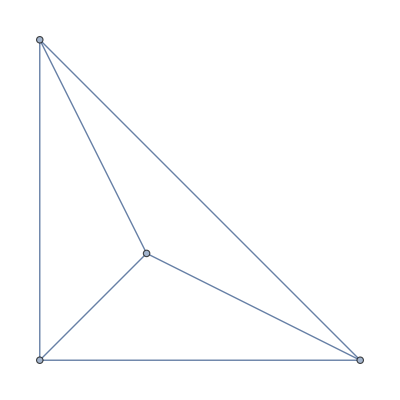
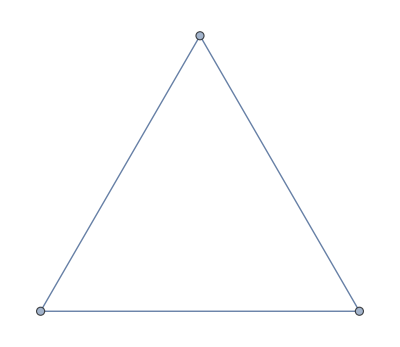
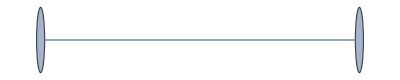
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Graph[EdgeList[allGraphs6[#,"graph"]],GraphLayout->"PlanarEmbedding"]&,Select[mp,Length[ListofVars[allGraphs6[#,"colofour"]]]==1&]]
```

```mathematica
Map[Graph[EdgeList[allGraphs6[#,"graph"]],GraphLayout->"PlanarEmbedding"]&,Select[mp,Length[ListofVars[allGraphs6[#,"colofour"]]]==5&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Graph[EdgeList[allGraphs6[#,"graph"]],GraphLayout->"PlanarEmbedding"]&,Select[mp,Length[ListofVars[allGraphs6[#,"colofour"]]]==8&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}